```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

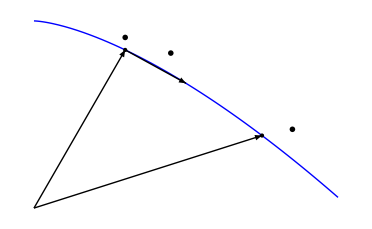

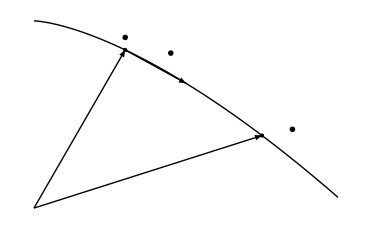

```mathematica
ClearAll[o, f, pair, g, oneParameterDifferentialFig1, x]

o = {0,0};
f = 3 - #^1.5 & ;
pair = {#,f[#]} &;


g[c_] :=Show[{
 Plot[
f[x], {x,0,2}, 
PlotStyle->{Thick, c},
Axes-> None
],
Graphics[{
Thick,Arrowheads[0.05],
Arrow[{o,pair[0.6]}],
Arrow[{o,pair[1.5]}],
Arrow[{pair[0.6],pair[1]}],
PointSize[Large],
Point[{0.6,f[0.6]}],
Point[{1.5, f[1.5]}],
Text[MaTeX["\\mathbf{x}(a)"], {0.6,f[0.6] + 0.2}],
Text[MaTeX["d\\mathbf{x}_a"], {0.8 + 0.1,f[0.8] + 0.2}],
Text[MaTeX["\\mathbf{x}(a + \\Delta a)"],{1.5 + 0.2, f[1.5] + 0.1}]
}]
}]

oneParameterDifferentialFig1 = g[Blue]
bwoneParameterDifferentialFig1 = g[Black]
```

```mathematica
peeters`exportForLatex["color/oneParameterDifferentialFig1", oneParameterDifferentialFig1]
peeters`exportForLatex["bw/oneParameterDifferentialFig1", bwoneParameterDifferentialFig1]
```

{color/oneParameterDifferentialFig1.eps,color/oneParameterDifferentialFig1pn.png}

{bw/oneParameterDifferentialFig1.eps,bw/oneParameterDifferentialFig1pn.png}